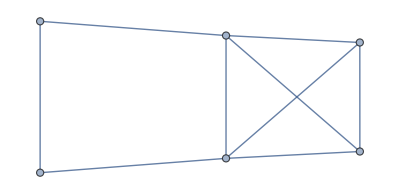

```mathematica
G=RandomGraph[DegreeGraphDistribution[{4,4,3,3,2,2}]]
```

```mathematica
SeedRandom[1]
G=RandomGraph[DegreeGraphDistribution[ConstantArray[3,50000]]];
Export["3_regular.s6",G]
```

3_regular.s6

```mathematica
SeedRandom[2]
G=RandomGraph[DegreeGraphDistribution[ConstantArray[3,50000]]];
Export["3_regular_2.s6",G]
```

3_regular_2.s6

```mathematica
SeedRandom[3]
G=RandomGraph[DegreeGraphDistribution[Join[ConstantArray[3,20000],ConstantArray[5,20000],ConstantArray[7,10000]]]];
Export["3_5_7_degree_distribution.s6",G]
```

3_5_7_degree_distribution.s6

```mathematica
SeedRandom[4]
G=RandomGraph[DegreeGraphDistribution[Join[ConstantArray[3,20000],ConstantArray[5,20000],ConstantArray[7,10000]]]];
Export["3_5_7_degree_distribution_2.s6",G]
```

3_5_7_degree_distribution_2.s6

```mathematica
SeedRandom[10]
G=RandomGraph[DegreeGraphDistribution[ConstantArray[6,50000]]];
Export["6_regular.s6",G];
```

```mathematica
"6_regular.s6"
```

```mathematica
SeedRandom[11]
G =RandomGraph[BernoulliGraphDistribution[5000000,1.05/5000000]];
Components = ConnectedComponents[G];
C1 = Subgraph[G,First[Components]];
VertexCount[C1]
C1Core =Subgraph[C1,First[KCoreComponents[C1,2]]];
VertexCount[C1Core]
Export["ergc_2core_1.s6",C1Core];
```

461028

21154

```mathematica
SeedRandom[12]
G =RandomGraph[BernoulliGraphDistribution[25000000,1.05/25000000]];
Components = ConnectedComponents[G];
C1 = Subgraph[G,First[Components]];
VertexCount[C1]
C1Core =Subgraph[C1,First[KCoreComponents[C1,2]]];
VertexCount[C1Core]
Export["ergc_2core_2.s6",C1Core];
```

2365541

118573

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]